```mathematica
a=Table[{x-1,FactorInteger[x]},{x,2,20}]//Grid
```

1 | {{2,1}}
2 | {{3,1}}
3 | {{2,2}}
4 | {{5,1}}
5 | {{2,1},{3,1}}
6 | {{7,1}}
7 | {{2,3}}
8 | {{3,2}}
9 | {{2,1},{5,1}}
10 | {{11,1}}
11 | {{2,2},{3,1}}
12 | {{13,1}}
13 | {{2,1},{7,1}}
14 | {{3,1},{5,1}}
15 | {{2,4}}
16 | {{17,1}}
17 | {{2,1},{3,2}}
18 | {{19,1}}
19 | {{2,2},{5,1}}

```mathematica
F[x_]:=Module[{f=FactorInteger[x]},
m=PrimePi[Max[f[[All,1]]]];
o=ConstantArray[0,m];
For[i=1,i≤Length[f],i++,
o[[PrimePi[f[[i,1]]]]]=f[[i,2]];];
Return[o]]
```

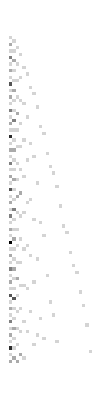

```mathematica
ArrayPlot[Table[F[x],{x,2,100}]]
```

```mathematica
G[{mi_,ma_},{mit_,mat_},radm_]:=Module[{o={}},
For[i=mi,i≤ma,i++,
f=FactorInteger[i];
lf=Length[f];
For[j=1,j≤lf,j++,
h=PrimePi[f[[j,1]]];
r=E^(f[[j,2]] radm);
(*r=Log[i];*)
If[mit<h<mat,AppendTo[o,Circle[{i,h},r]]];
];
];
Return[o];
]
```

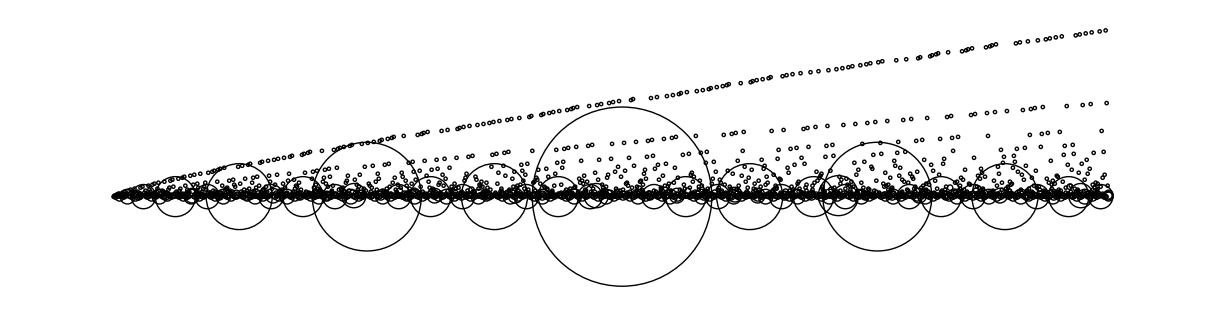

```mathematica
Graphics[G[{2,1000},{0,500},.5]]
```